```mathematica
FindRoot[(2*a/(2*b^2*a^2+  (1- b^2*a^2)/2*x))*Exp[-x/(4-x)/(b^2*a^2)] - 0.99*1/(a*b^2),{x,1000}]
```

FindRoot::nlnum: The function value {-0.99/a\ b^2 + 2.\ « 18 »^« 18 »/« 1 »\ a/2.\ a^2\ b^2 + 500.\ (« 1 »)} is not a list of numbers with dimensions {1} at {x} = {1000.}.

FindRoot[((2 a) ⅇ^(-x/((4-x) (b^2 a^2))))/(2 b^2 a^2+1/2 (1-b^2 a^2) x)-0.99/(a b^2),{x,1000}]

```mathematica
help plot
```

help plot

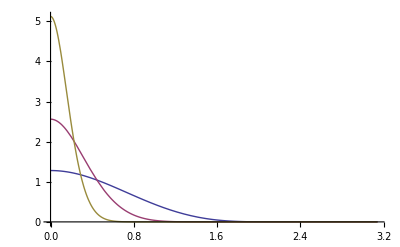

```mathematica
Plot[Evaluate[Table[2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2],{n,1,3}]],{x,0,Pi},PlotRange->All]
```

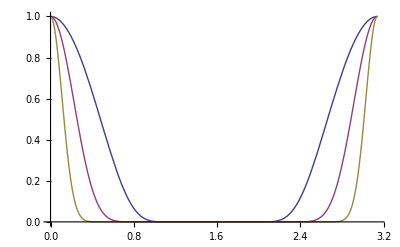

```mathematica
Plot[Evaluate[Table[Exp[-(Tan[x]/(1.25/2^n))^2],{n,1,3}]],{x,0,Pi},PlotRange->All]
```

```mathematica
FindRoot[Evaluate[Table[2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2],{n,1,3}]],{x,0,Pi}]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[{ⅇ^-2.56\ « 1 »^2/1.39063  - 0.609375\ Cos[x], ⅇ^« 1 »/2\ (« 11 »  - « 1 »), ⅇ^-40.96\ « 1 »/4\ (1.02441  - 0.975586\ Cos[x])}, {x, 0, π}].

FindRoot[{(ⅇ^(-2.56 Tan[x/2]^2))/(1.39063-0.609375 Cos[x]),(ⅇ^(-10.24 Tan[x/2]^2))/(2 (1.09766-0.902344 Cos[x])),(ⅇ^(-40.96 Tan[x/2]^2))/(4 (1.02441-0.975586 Cos[x]))},{x,0,π}]

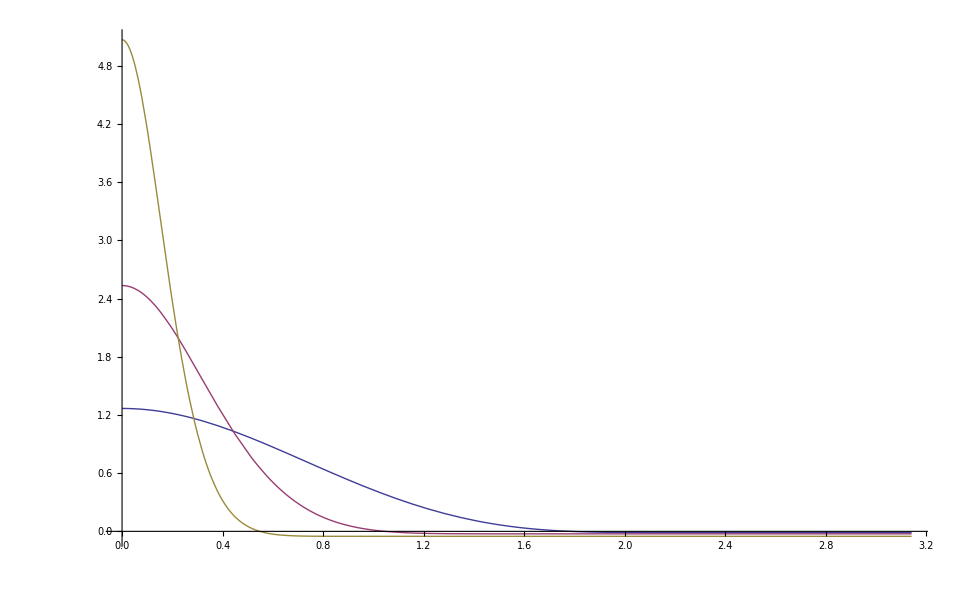

```mathematica
Plot[Evaluate[Table[2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2] - 0.01*1/1.25^2/(1/2^n),{n,1,3}]],{x,0,Pi}, PlotRange->All]
```

```mathematica
FindRoot[2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2] - 0.01*1/1.25^2/(1/2^n),{x,0,Pi}]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[-0.0064\ 2^n + 2^1 - n\ ⅇ^-0.64\ « 1 »\ « 1 »^2/1 + 1.5625\ 2^Times[« 2 »] + (-1 + Times[« 2 »])\ Cos[x], {n, 1, 3}, {x, 0, π}].

FindRoot[-0.0064 2^n+(2^(1-n) ⅇ^(-0.64 2^(2 n) Tan[x/2]^2))/(1+1.5625 2^(-2 n)+(-1+1.5625 2^(-2 n)) Cos[x]),{n,1,3},{x,0,π}]

```mathematica
FindRoot[2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2] - 0.01*1/1.25^2/(1/2^n),{x,0,Pi}]
```

FindRoot::nlnum: The function value {-0.0064\ 2.^n + 2.^1.  - 1.\ n\ 2.71828^0.\ 2.^2.\ n/1.  + 1.5625\ 2.^Times[« 2 »] + 1.\ (-1. + Times[« 2 »])} is not a list of numbers with dimensions {1} at {x} = {0.}.

FindRoot[(2 ⅇ^(-(Tan[x/2]/(1.25/2^n))^2))/(2^n (((1.25/2^n)^2-1) Cos[x]+1+(1.25/2^n)^2))-0.01/(1.25^2/2^n),{x,0,π}]

```mathematica
n = 1
```

1

```mathematica
n
```

1

```mathematica
FindRoot[2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2] - 0.01*1/1.25^2/(1/2^n),{x,0,Pi}]
```

{x→1.78468}

```mathematica
n = 7
R = FindRoot[2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2] - 0.1*1/1.25^2/(1/2^n),{x,0,Pi}]
```

7

{x→0.023267}

```mathematica
0.02326704820962144*180/Pi
```

1.3331

```mathematica
x
```

x

```mathematica
R
```

{x→0.017403}

```mathematica
n = 2
R = FindRoot[2*(1/2^n)/(((1/2^n)^2-1)*Cos[x]+1+(1/2^n)^2)*Exp[-(Tan[x/2]/(1/2^n))^2] - 2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2]  ,{x,0,Pi}]
```

2

{x→3.14159}

8

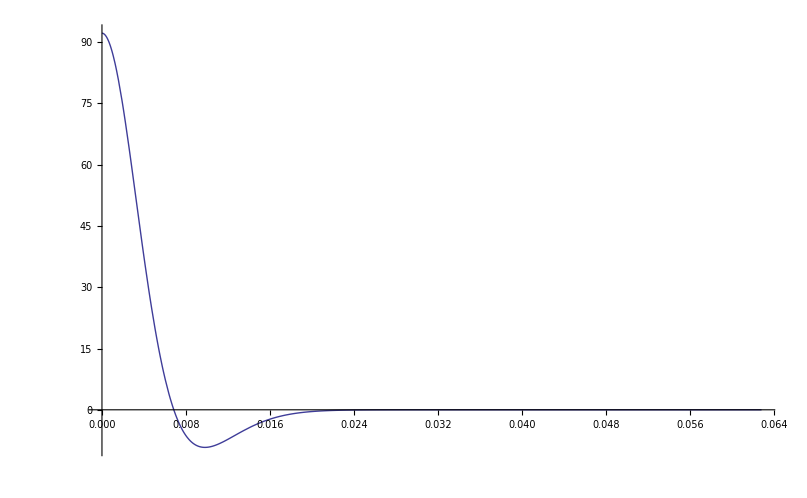

```mathematica
n = 8
R =Plot[2*(1/2^n)/(((1/2^n)^2-1)*Cos[x]+1+(1/2^n)^2)*Exp[-(Tan[x/2]/(1/2^n))^2] - 2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2]  ,{x,0,Pi/50},PlotRange->All]
```

8

{x→0.0138534}

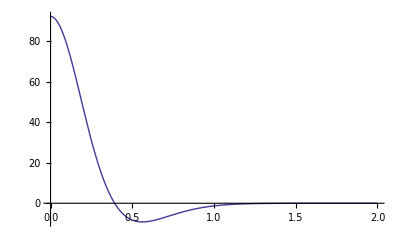

```mathematica
n = 8
R  = FindRoot[2*(1/2^n)/(((1/2^n)^2-1)*Cos[x]+1+(1/2^n)^2)*Exp[-(Tan[x/2]/(1/2^n))^2] - 2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x]+1+(1.25/2^n)^2)*Exp[-(Tan[x/2]/(1.25/2^n))^2] == -0.05*(2^n - 2^n/(1.25)^2)  ,{x,0.015}]

Plot[2*(1/2^n)/(((1/2^n)^2-1)*Cos[x*Pi/180]+1+(1/2^n)^2)*Exp[-(Tan[x*Pi/180/2]/(1/2^n))^2] - 2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x*Pi/180]+1+(1.25/2^n)^2)*Exp[-(Tan[x*Pi/180/2]/(1.25/2^n))^2]  ,{x,0,2},PlotRange->All]
```

```mathematica
0.013853411421573002*180/Pi
```

0.793742

9

{x→0.196075}

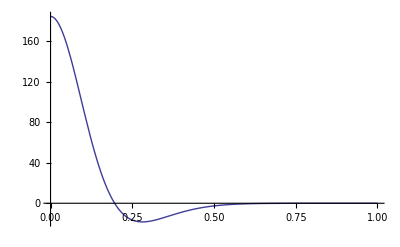

```mathematica
n = 9
R  = FindRoot[2*(1/2^n)/(((1/2^n)^2-1)*Cos[x*Pi/180]+1+(1/2^n)^2)*Exp[-(Tan[x*Pi/180/2]/(1/2^n))^2] - 2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x*Pi/180]+1+(1.25/2^n)^2)*Exp[-(Tan[x*Pi/180/2]/(1.25/2^n))^2]   ,{x,0.1}]

Plot[2*(1/2^n)/(((1/2^n)^2-1)*Cos[x*Pi/180]+1+(1/2^n)^2)*Exp[-(Tan[x*Pi/180/2]/(1/2^n))^2] - 2*(1/2^n)/(((1.25/2^n)^2-1)*Cos[x*Pi/180]+1+(1.25/2^n)^2)*Exp[-(Tan[x*Pi/180/2]/(1.25/2^n))^2]  ,{x,0,1},PlotRange->All]
```